```mathematica
maxHCalc[xval_,tsnondval_, fval_,βpval_]:=Module[{nondeqns, subs,nondbcsb, nondbcsc,solb, solc,x,tsnond,βp,f,fnond,h,m,v,t,maxh },
nondeqns={h'[t] == v[t], v'[t] == (fnond-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, m'[t] == -fnond};
subs = {x-> xval, tsnond-> tsnondval, βp-> βpval, f-> fval};
nondbcsb = {h[0] == 0, v[0] ==0, m[0] == 1};
solb=NDSolve[({nondeqns, nondbcsb}/.fnond-> f/.subs)//Flatten,{h[t],m[t],v[t]},{t, 0, tsnond}/. subs];
nondbcsc = {h[t] == (h[t]/.solb[[1]])/.t-> (tsnond/.subs),
 v[t] == (v[t]/.solb[[1]])/.t-> (tsnond/.subs),
m[t] == (m[t]/.solb[[1]])/.t-> (tsnond/.subs)};
solc=Quiet[NDSolve[({nondeqns, nondbcsc}/.fnond-> 0/.subs)//Flatten,{h[t],m[t],v[t]},{t,  tsnond, 20*tsnond}/.subs]];
(*g1=Plot[ (h[t]/.solb[[1]]),{t,solb[[1]][[1]][[2]][[0]]["Domain"][[1]][[1]], solb[[1]][[1]][[2]][[0]]["Domain"][[1]][[2]]},PlotStyle->Red];
g2=Plot[ (h[t]/.solc[[1]]),{t,solc[[1]][[1]][[2]][[0]]["Domain"][[1]][[1]], solc[[1]][[1]][[2]][[0]]["Domain"][[1]][[2]]}];*)
maxh=Maximize[{h[t]/.solc[[1]], t>solc[[1]][[1]][[2]][[0]]["Domain"][[1]][[1]], t<solc[[1]][[1]][[2]][[0]]["Domain"][[1]][[2]]},t][[1]]]
(*
Show[{g1,g2},PlotRange-> {0,All}]*)
```

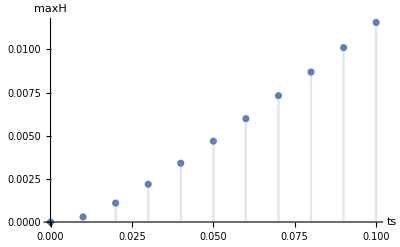

```mathematica
(*Max H as function of ts*)
DiscretePlot[
maxHCalc[180, ts, 3, 50],{ts,0.0, 0.1,0.01}, AxesLabel->{"ts","maxH"}, AxesOrigin->{0,0}]
```

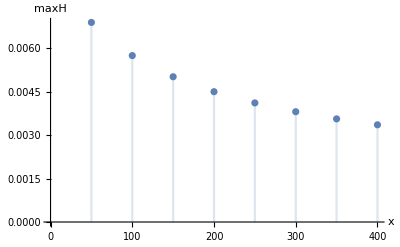

```mathematica
(*Max H as function of x*)
DiscretePlot[
maxHCalc[x, 0.05, 3, 50],{x,50,400,50}, AxesLabel->{"x","maxH"}, AxesOrigin->{0,0}]
```

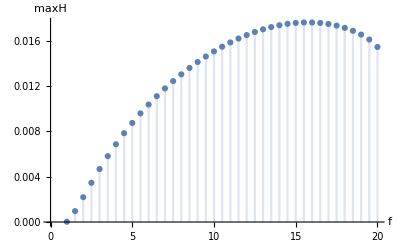

```mathematica
(*Max H as function of fnond*)
DiscretePlot[
maxHCalc[180, 0.05, f, 50],{f,1,20,0.5}, AxesLabel->{"f","maxH"}, AxesOrigin->{0,0}]
```

7/24

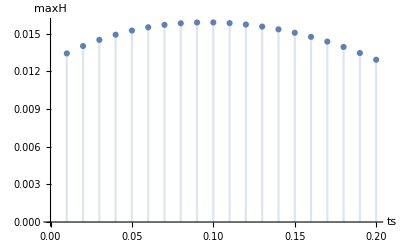

```mathematica
(*Max H as function of fnond*)
impulse = 35000/(60*2000) (*non dimensionalized*)
DiscretePlot[
maxHCalc[90, ts, impulse/ts, 50],{ts,0.01,0.2,0.01}, AxesLabel->{"ts","maxH"}, AxesOrigin->{0,0}]
```

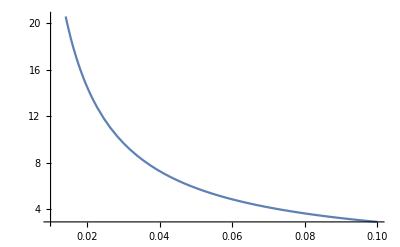

```mathematica
Plot[impulse/ts, {ts,0.01,0.1}]
```

```mathematica
tbl=Table[{x,ts,maxHCalc[x, ts, impulse/ts, 50]},{x,50,400,50},{ts,0.01,0.1,0.02}];
ListContourPlot[tbl]
```

-Graphics-

```mathematica
xlist = Table[x,{x,50,400,50}]
tslist = Table[ts,{ts,0.01,0.1,0.02}]
```

{50,100,150,200,250,300,350,400}

{0.01,0.03,0.05,0.07,0.09}

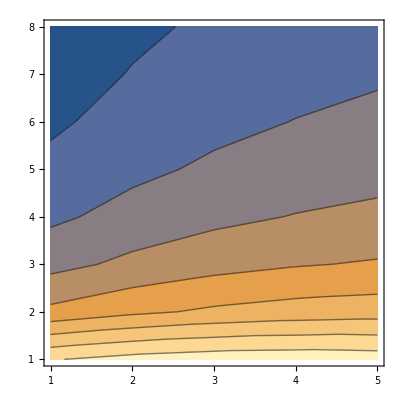

```mathematica
tbl=Table[maxHCalc[x, ts, impulse/ts, 50],{x,xlist},{ts,tslist}];
ListContourPlot[tbl]
```

```mathematica
DiscretePlot3D[maxHCalc[x,ts,impulse/ts, 50],{x,50,400,50},{ts,0.01,0.2,0.02}, Joined->True]
```

-Graphics3D-

```mathematica
impulse = 0.4
DiscretePlot3D[{0.02,maxHCalc[x,impulse/f,f, 50]},{x,50,400,50},{f,1,5,0.5}, Joined->True]
```

0.4

-Graphics3D-

```mathematica
impulse = 0.3
DiscretePlot3D[maxHCalc[x,impulse/f,f, 50],{x,50,400,50},{f,1,5,0.5}, Joined->True]
```

0.3

-Graphics3D-

```mathematica
Clear[ts]
```

```mathematica
impulse
```

0.3

```mathematica
maxHCalc[100,0.01, impulse/0.01,50]
```

0.0127504

```mathematica
maxHCalc[180,tsval/.tsval-> 0.05,N[impulse/tsval/.tsval-> 0.05],50]
```

0.0103813

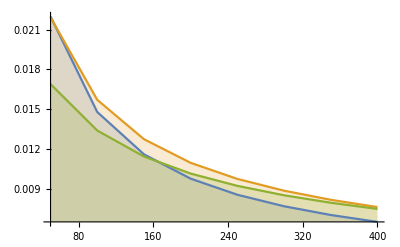

```mathematica
DiscretePlot[{maxHCalc[x,0.05,impulse/0.05,50], maxHCalc[x,0.1,impulse/0.1,50],maxHCalc[x,0.2,impulse/0.2,50]},{x,50,400,50}, Joined->True]
```

```mathematica
Needs["NumericalCalculus`"]
NSeries[maxHCalc[xval,impulse/2,2, 50],{xval,180,2},WorkingPrecision->17]
```

NDSolve::nlnum: The function value {0.0000152831,-2.,-1+1.00003 (2-2.33572×10^-10 xval)} is not a list of numbers with dimensions {3} at {t,h[t],m[t],v[t]} = {0.0000152831,0.,0.999969,0.0000152831}.

InterpolatingFunction::dmval: Input value {0.15} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ReplaceAll::reps: {h'[t]==v[t],v'[t]==-1-(ⅇ^(-50 h[t]) xval v[t]^2)/m[t],m'[t]==0,h[0.15]==0.,v[0.15]==0.15,m[0.15]==0.7} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {h'[t]==v[t],v'[t]==-1-(181. ⅇ^(-50 h[t]) v[t]^2)/m[t],m'[t]==0,h[0.15]==0.,v[0.15]==0.15,m[0.15]==0.7} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h'[t]==v[t],v'[t]==-1.-(181. 2.7182818284590452^(-50. h[t]) v[t]^2)/m[t],m'[t]==0,h[0.15]==0.,v[0.15]==0.15,m[0.15]==0.7} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NSeries[{h[t]/.{h'[t]==v[t],v'[t]==-1-(ⅇ^(-50 h[t]) xval v[t]^2)/m[t],m'[t]==0,h[0.15]==0.,v[0.15]==0.15,m[0.15]==0.7},t>Domain⟦1⟧,t<Domain⟦2⟧},{xval,180,2},WorkingPrecision→17]

```mathematica
maxHCalcImp[xval_,impval_,fval_,βpval_]:= maxHCalc[xval,N[impval/fval],fval,βpval]
```

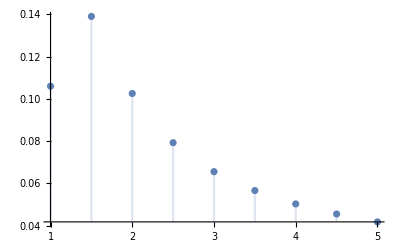

```mathematica
DiscretePlot[maxHCalcImp[180,0.9,f,50],{f,1,5,0.5}]
```

```mathematica
NSeries[maxHCalcImp[180,impulse,fval, 50],{fval,2,1},WorkingPrecision->17]
```

NDSolve::ndnl: Endpoint 0.3/fval in {t,0.,0.3/fval} is not a real number.

ReplaceAll::reps: {h'[t]==v[t],v'[t]==-1+(fval-180 ⅇ^Times[«2»] v[«1»]^2)/m[t],m'[t]==-fval,h[0]==0,v[0]==0,m[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h'[0.3/fval]==v[0.3/fval],v'[0.3/fval]==-1+(fval-180 ⅇ^Times[«2»] v[«1»]^2)/m[0.3 Power[«2»]],m'[0.3/fval]==-fval,h[0]==0,v[0]==0,m[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h'[t]==v[t],v'[t]==-1+(fval-180 ⅇ^Times[«2»] v[«1»]^2)/m[t],m'[t]==-fval,h[0]==0,v[0]==0,m[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

NSeries[{h[t]/.{h'[t]==v[t],v'[t]==-1-(180 ⅇ^(-50 h[t]) v[t]^2)/m[t],m'[t]==0,h[0.3/fval]==(h[0.3/fval]/.{h'[0.3/fval]==v[0.3/fval],v'[0.3/fval]==-1+(fval-180 ⅇ^(-50 h[0.3/fval]) v[0.3/fval]^2)/m[0.3/fval],m'[0.3/fval]==-fval,h[0]==0,v[0]==0,m[0]==1}),v[0.3/fval]==(v[0.3/fval]/.{h'[0.3/fval]==v[0.3/fval],v'[0.3/fval]==-1+(fval-180 ⅇ^(-50 h[0.3/fval]) v[0.3/fval]^2)/m[0.3/fval],m'[0.3/fval]==-fval,h[0]==0,v[0]==0,m[0]==1}),m[0.3/fval]==(m[0.3/fval]/.{h'[0.3/fval]==v[0.3/fval],v'[0.3/fval]==-1+(fval-180 ⅇ^(-50 h[0.3/fval]) v[0.3/fval]^2)/m[0.3/fval],m'[0.3/fval]==-fval,h[0]==0,v[0]==0,m[0]==1})},t>Domain⟦1⟧,t<Domain⟦2⟧},{fval,2,1},WorkingPrecision→17]

```mathematica
NSeries[maxHCalc[180,impulse/fval,fval, 50],{fval,2,1},WorkingPrecision->17]
```

NDSolve::ndnl: Endpoint 0.3/fval in {t,0.,0.3/fval} is not a real number.

ReplaceAll::reps: {h'[t]==v[t],v'[t]==-1+(fval-180 ⅇ^Times[«2»] v[«1»]^2)/m[t],m'[t]==-fval,h[0]==0,v[0]==0,m[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h'[0.3/fval]==v[0.3/fval],v'[0.3/fval]==-1+(fval-180 ⅇ^Times[«2»] v[«1»]^2)/m[0.3 Power[«2»]],m'[0.3/fval]==-fval,h[0]==0,v[0]==0,m[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h'[t]==v[t],v'[t]==-1+(fval-180 ⅇ^Times[«2»] v[«1»]^2)/m[t],m'[t]==-fval,h[0]==0,v[0]==0,m[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

NSeries[{h[t]/.{h'[t]==v[t],v'[t]==-1-(180 ⅇ^(-50 h[t]) v[t]^2)/m[t],m'[t]==0,h[0.3/fval]==(h[0.3/fval]/.{h'[0.3/fval]==v[0.3/fval],v'[0.3/fval]==-1+(fval-180 ⅇ^(-50 h[0.3/fval]) v[0.3/fval]^2)/m[0.3/fval],m'[0.3/fval]==-fval,h[0]==0,v[0]==0,m[0]==1}),v[0.3/fval]==(v[0.3/fval]/.{h'[0.3/fval]==v[0.3/fval],v'[0.3/fval]==-1+(fval-180 ⅇ^(-50 h[0.3/fval]) v[0.3/fval]^2)/m[0.3/fval],m'[0.3/fval]==-fval,h[0]==0,v[0]==0,m[0]==1}),m[0.3/fval]==(m[0.3/fval]/.{h'[0.3/fval]==v[0.3/fval],v'[0.3/fval]==-1+(fval-180 ⅇ^(-50 h[0.3/fval]) v[0.3/fval]^2)/m[0.3/fval],m'[0.3/fval]==-fval,h[0]==0,v[0]==0,m[0]==1})},t>Domain⟦1⟧,t<Domain⟦2⟧},{fval,2,1},WorkingPrecision→17]

```mathematica
tbl=Table[{{xval, impval, fval},maxHCalcImp[xval, impval, fval, 50]},{xval, 100,300,50},{impval,0.3,0.9,0.2},{fval,1,5,0.5}];
```

```mathematica
tbl2=Flatten[tbl,2];
interp = Interpolation[tbl2]
```

InterpolatingFunction[{{100., 300.}, {0.3, 0.9}, {1., 5.}}, <>]

InterpolatingFunction[{{100., 300.}, {0.3, 0.9}, {1., 5.}}, <>]

```mathematica
f
```

f

```mathematica
FindMaximum[{maxHCalcImp[200, 0.4, f, 50],f>1,f<3},{f,2}];
```

NDSolve::ndnl: Endpoint 0.4/f in {t$281184,0.,0.4/f} is not a real number.

ReplaceAll::reps: {h$281184'[t$281184]==v$281184[t$281184],v$281184'[t$281184]==-1+(f-200 ⅇ^Times[«2»] v$281184[«1»]^2)/m$281184[t$281184],m$281184'[t$281184]==-f,h$281184[0]==0,v$281184[0]==0,m$281184[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h$281184'[0.4/f]==v$281184[0.4/f],v$281184'[0.4/f]==-1+(f-200 ⅇ^Times[«2»] v$281184[«1»]^2)/m$281184[0.4 Power[«2»]],m$281184'[0.4/f]==-f,h$281184[0]==0,v$281184[0]==0,m$281184[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h$281184'[t$281184]==v$281184[t$281184],v$281184'[t$281184]==-1+(f-200 ⅇ^Times[«2»] v$281184[«1»]^2)/m$281184[t$281184],m$281184'[t$281184]==-f,h$281184[0]==0,v$281184[0]==0,m$281184[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value {«1»} is not a real number at {f} = {2.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindMaximum::nrnum: The function value {«1»} is not a real number at {f} = {1.99999}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[-{h$281184[t$281184]/.{(«1»)^(«1»)[«1»]==v$281184[«1»],(«1»)^(«1»)[«1»]==Plus[«2»],(«1»)^(«1»)[«1»]==0,h$281184[«1»]==ReplaceAll[«2»],v$281184[«1»]==ReplaceAll[«2»],m$281184[«1»]==ReplaceAll[«2»]},t$281184>Domain⟦1⟧,t$281184<Domain⟦2⟧}],Block},{0,{{{},1,0,Hold[f],0,0}}},{{{«1»},«1»}},«1»,{904,«6»,None},{None,None,None}] failed at {2.}.

FindMaximum[{maxHCalcImp[200,0.4,f,50],f>1,f<3},{f,2}]

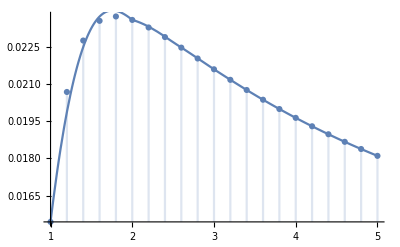

```mathematica
Show[DiscretePlot[maxHCalcImp[200, 0.5, f, 50],{f,1,5,0.2}],Plot[ interp[200, 0.5, f],{f,1,5}]]
```

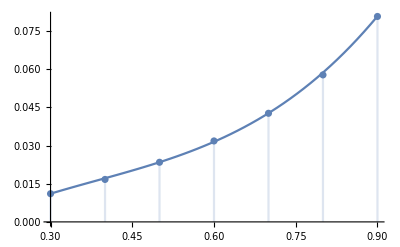

```mathematica
Show[DiscretePlot[maxHCalcImp[200, imp, 2.1, 50],{imp,0.3,0.9,0.1}],Plot[ interp[200, imp, 2.1],{imp,0.3,0.9}]]
```

```mathematica
g1=DiscretePlot3D[maxHCalcImp[100, imp,f,50],{imp,0.3,0.9,0.1},{f,1,5,0.5}];
g2=Plot3D[interp[100,imp,f],{imp,0.3,0.9},{f,1,5},PlotRange->All];
Show[{g1,g2},PlotRange-> All]
```

-Graphics3D-

```mathematica
Show[DiscretePlot[maxHCalcImp[180, 0.4, f, 50],{f,1,5,0.2}],Plot[ interp[180, 0.4, f, 50],{f,1,5}]]
```

```mathematica
Do[
Print[FindMaximum[{interp[100,imp,f], f<5, f>1},{f,2}]],
{imp, 0.3,0.9,0.1}]
```

{0.0157228,{f→2.81523}}

{0.0483644,{f→1.61794}}

{0.0365245,{f→2.03111}}

{0.0433406,{f→3.29156}}

{0.0898648,{f→1.67796}}

{0.266277,{f→1.54968}}

{0.617972,{f→1.52312}}

```mathematica
FindArgMax[{interp[100,0.4,f], f<5, f>1},{f,2}]
```

{1.61794}

```mathematica
Do[
Print[FindMaximum[{interp[180,imp,f,50], f<5, f>1},{f,2}]],
{imp, 0.3,0.9,0.1}]
```

{0.0119187,{f→2.16637}}

{0.0176808,{f→2.06728}}

{0.0251409,{f→1.79705}}

{0.035584,{f→1.68574}}

{0.0510431,{f→1.57467}}

{0.0734895,{f→1.49633}}

InterpolatingFunction::dmval: Input value {180,0.9,2.,50} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180,0.9,1.99999,50} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180,0.9,2.00001,50} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.104698,{f→1.44796}}

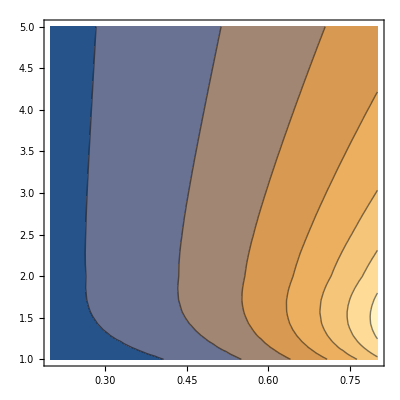

```mathematica
ContourPlot[interp[180,imp,fval,50],{imp,0.2,0.8},{fval,1,5}]
```

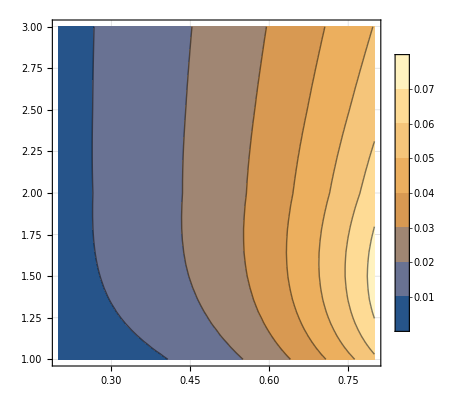

```mathematica
ContourPlot[interp[180,imp,fval,50],{imp,0.2,0.8},{fval,1,3},GridLines->Automatic,PlotLegends->Automatic]
```

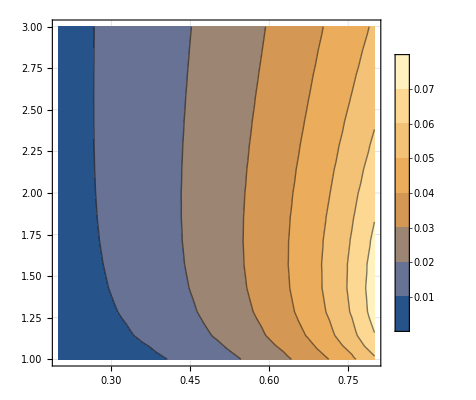

```mathematica
ContourPlot[maxHCalcImp[180, imp,f,50],{imp,0.2,0.8},{f,1,3},MaxRecursion->0,GridLines->Automatic,PlotLegends->Automatic]
```

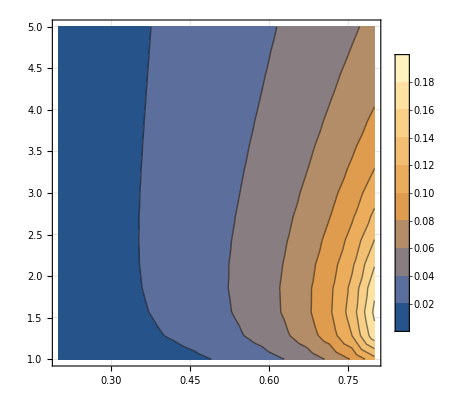

```mathematica
ContourPlot[maxHCalcImp[100, imp,f,50],{imp,0.2,0.8},{f,1,5},MaxRecursion->0,GridLines->Automatic,PlotLegends->Automatic]
```

```mathematica
exporttbl=Table[{xval, impval, fval,betaval,maxHCalcImp[xval, impval, fval, betaval]},{xval, 100,300,50},{impval,0.3,0.9,0.2},{fval,1,5,0.2},{betaval,{50}}];
```

```mathematica
Flatten[exporttbl,3]//TableForm
```

100 | 0.3 | 1. | 50 | 0.00540524
100 | 0.3 | 1.2 | 50 | 0.0102523
100 | 0.3 | 1.4 | 50 | 0.0126313
100 | 0.3 | 1.6 | 50 | 0.0139543
100 | 0.3 | 1.8 | 50 | 0.0147289
100 | 0.3 | 2. | 50 | 0.0151904
100 | 0.3 | 2.2 | 50 | 0.0154626
100 | 0.3 | 2.4 | 50 | 0.0156156
100 | 0.3 | 2.6 | 50 | 0.0156915
100 | 0.3 | 2.8 | 50 | 0.0157166
100 | 0.3 | 3. | 50 | 0.0157078
100 | 0.3 | 3.2 | 50 | 0.0156764
100 | 0.3 | 3.4 | 50 | 0.0156298
100 | 0.3 | 3.6 | 50 | 0.0155733
100 | 0.3 | 3.8 | 50 | 0.0155104
100 | 0.3 | 4. | 50 | 0.0154437
100 | 0.3 | 4.2 | 50 | 0.0153749
100 | 0.3 | 4.4 | 50 | 0.0153054
100 | 0.3 | 4.6 | 50 | 0.0152359
100 | 0.3 | 4.8 | 50 | 0.0151671
100 | 0.3 | 5. | 50 | 0.0150995
100 | 0.5 | 1. | 50 | 0.0209826
100 | 0.5 | 1.2 | 50 | 0.0295838
100 | 0.5 | 1.4 | 50 | 0.0336137
100 | 0.5 | 1.6 | 50 | 0.0355362
100 | 0.5 | 1.8 | 50 | 0.0363405
100 | 0.5 | 2. | 50 | 0.0365197
100 | 0.5 | 2.2 | 50 | 0.0363422
100 | 0.5 | 2.4 | 50 | 0.0359614
100 | 0.5 | 2.6 | 50 | 0.0354676
100 | 0.5 | 2.8 | 50 | 0.0349155
100 | 0.5 | 3. | 50 | 0.0343382
100 | 0.5 | 3.2 | 50 | 0.0337561
100 | 0.5 | 3.4 | 50 | 0.0331815
100 | 0.5 | 3.6 | 50 | 0.032622
100 | 0.5 | 3.8 | 50 | 0.0320817
100 | 0.5 | 4. | 50 | 0.0315629
100 | 0.5 | 4.2 | 50 | 0.0310665
100 | 0.5 | 4.4 | 50 | 0.0305925
100 | 0.5 | 4.6 | 50 | 0.0301407
100 | 0.5 | 4.8 | 50 | 0.0297102
100 | 0.5 | 5. | 50 | 0.0293002
100 | 0.7 | 1. | 50 | 0.057908
100 | 0.7 | 1.2 | 50 | 0.0774878
100 | 0.7 | 1.4 | 50 | 0.0862734
100 | 0.7 | 1.6 | 50 | 0.0890534
100 | 0.7 | 1.8 | 50 | 0.0885198
100 | 0.7 | 2. | 50 | 0.0862588
100 | 0.7 | 2.2 | 50 | 0.0831859
100 | 0.7 | 2.4 | 50 | 0.0798157
100 | 0.7 | 2.6 | 50 | 0.0764277
100 | 0.7 | 2.8 | 50 | 0.073166
100 | 0.7 | 3. | 50 | 0.0700981
100 | 0.7 | 3.2 | 50 | 0.067249
100 | 0.7 | 3.4 | 50 | 0.0646208
100 | 0.7 | 3.6 | 50 | 0.062204
100 | 0.7 | 3.8 | 50 | 0.0599837
100 | 0.7 | 4. | 50 | 0.0579431
100 | 0.7 | 4.2 | 50 | 0.0560653
100 | 0.7 | 4.4 | 50 | 0.0543342
100 | 0.7 | 4.6 | 50 | 0.0527352
100 | 0.7 | 4.8 | 50 | 0.0512548
100 | 0.7 | 5. | 50 | 0.0498811
100 | 0.9 | 1. | 50 | 0.399786
100 | 0.9 | 1.2 | 50 | 0.566345
100 | 0.9 | 1.4 | 50 | 0.615765
100 | 0.9 | 1.6 | 50 | 0.609375
100 | 0.9 | 1.8 | 50 | 0.571658
100 | 0.9 | 2. | 50 | 0.516679
100 | 0.9 | 2.2 | 50 | 0.454148
100 | 0.9 | 2.4 | 50 | 0.391043
100 | 0.9 | 2.6 | 50 | 0.332091
100 | 0.9 | 2.8 | 50 | 0.280055
100 | 0.9 | 3. | 50 | 0.236099
100 | 0.9 | 3.2 | 50 | 0.200226
100 | 0.9 | 3.4 | 50 | 0.171691
100 | 0.9 | 3.6 | 50 | 0.149349
100 | 0.9 | 3.8 | 50 | 0.13194
100 | 0.9 | 4. | 50 | 0.118305
100 | 0.9 | 4.2 | 50 | 0.107492
100 | 0.9 | 4.4 | 50 | 0.0987782
100 | 0.9 | 4.6 | 50 | 0.091633
100 | 0.9 | 4.8 | 50 | 0.0856755
100 | 0.9 | 5. | 50 | 0.0806316
150 | 0.3 | 1. | 50 | 0.00496713
150 | 0.3 | 1.2 | 50 | 0.00901287
150 | 0.3 | 1.4 | 50 | 0.0108624
150 | 0.3 | 1.6 | 50 | 0.0118292
150 | 0.3 | 1.8 | 50 | 0.0123546
150 | 0.3 | 2. | 50 | 0.012636
150 | 0.3 | 2.2 | 50 | 0.0127746
150 | 0.3 | 2.4 | 50 | 0.0128263
150 | 0.3 | 2.6 | 50 | 0.0128239
150 | 0.3 | 2.8 | 50 | 0.0127876
150 | 0.3 | 3. | 50 | 0.0127299
150 | 0.3 | 3.2 | 50 | 0.0126591
150 | 0.3 | 3.4 | 50 | 0.0125805
150 | 0.3 | 3.6 | 50 | 0.0124977
150 | 0.3 | 3.8 | 50 | 0.012413
150 | 0.3 | 4. | 50 | 0.012328
150 | 0.3 | 4.2 | 50 | 0.0122439
150 | 0.3 | 4.4 | 50 | 0.0121614
150 | 0.3 | 4.6 | 50 | 0.0120809
150 | 0.3 | 4.8 | 50 | 0.0120027
150 | 0.3 | 5. | 50 | 0.011927
150 | 0.5 | 1. | 50 | 0.0175858
150 | 0.5 | 1.2 | 50 | 0.0240237
150 | 0.5 | 1.4 | 50 | 0.0267465
150 | 0.5 | 1.6 | 50 | 0.0278887
150 | 0.5 | 1.8 | 50 | 0.0282412
150 | 0.5 | 2. | 50 | 0.028176
150 | 0.5 | 2.2 | 50 | 0.027886
150 | 0.5 | 2.4 | 50 | 0.0274767
150 | 0.5 | 2.6 | 50 | 0.0270082
150 | 0.5 | 2.8 | 50 | 0.0265151
150 | 0.5 | 3. | 50 | 0.0260176
150 | 0.5 | 3.2 | 50 | 0.0255277
150 | 0.5 | 3.4 | 50 | 0.025052
150 | 0.5 | 3.6 | 50 | 0.0245942
150 | 0.5 | 3.8 | 50 | 0.024156
150 | 0.5 | 4. | 50 | 0.0237381
150 | 0.5 | 4.2 | 50 | 0.0233403
150 | 0.5 | 4.4 | 50 | 0.022962
150 | 0.5 | 4.6 | 50 | 0.0226025
150 | 0.5 | 4.8 | 50 | 0.0222609
150 | 0.5 | 5. | 50 | 0.0219361
150 | 0.7 | 1. | 50 | 0.0429922
150 | 0.7 | 1.2 | 50 | 0.0541722
150 | 0.7 | 1.4 | 50 | 0.0581516
150 | 0.7 | 1.6 | 50 | 0.0587896
150 | 0.7 | 1.8 | 50 | 0.0578203
150 | 0.7 | 2. | 50 | 0.0561203
150 | 0.7 | 2.2 | 50 | 0.0541368
150 | 0.7 | 2.4 | 50 | 0.0520959
150 | 0.7 | 2.6 | 50 | 0.0501082
150 | 0.7 | 2.8 | 50 | 0.0482244
150 | 0.7 | 3. | 50 | 0.0464641
150 | 0.7 | 3.2 | 50 | 0.0448309
150 | 0.7 | 3.4 | 50 | 0.0433204
150 | 0.7 | 3.6 | 50 | 0.0419248
150 | 0.7 | 3.8 | 50 | 0.0406348
150 | 0.7 | 4. | 50 | 0.0394411
150 | 0.7 | 4.2 | 50 | 0.0383345
150 | 0.7 | 4.4 | 50 | 0.0373067
150 | 0.7 | 4.6 | 50 | 0.0363502
150 | 0.7 | 4.8 | 50 | 0.0354581
150 | 0.7 | 5. | 50 | 0.0346243
150 | 0.9 | 1. | 50 | 0.159136
150 | 0.9 | 1.2 | 50 | 0.238785
150 | 0.9 | 1.4 | 50 | 0.249294
150 | 0.9 | 1.6 | 50 | 0.226699
150 | 0.9 | 1.8 | 50 | 0.193963
150 | 0.9 | 2. | 50 | 0.162802
150 | 0.9 | 2.2 | 50 | 0.137564
150 | 0.9 | 2.4 | 50 | 0.118468
150 | 0.9 | 2.6 | 50 | 0.104211
150 | 0.9 | 2.8 | 50 | 0.0934046
150 | 0.9 | 3. | 50 | 0.0850021
150 | 0.9 | 3.2 | 50 | 0.0782933
150 | 0.9 | 3.4 | 50 | 0.0728069
150 | 0.9 | 3.6 | 50 | 0.0682271
150 | 0.9 | 3.8 | 50 | 0.064337
150 | 0.9 | 4. | 50 | 0.0609841
150 | 0.9 | 4.2 | 50 | 0.0580583
150 | 0.9 | 4.4 | 50 | 0.0554779
150 | 0.9 | 4.6 | 50 | 0.0531816
150 | 0.9 | 4.8 | 50 | 0.0511218
150 | 0.9 | 5. | 50 | 0.0492615
200 | 0.3 | 1. | 50 | 0.00462933
200 | 0.3 | 1.2 | 50 | 0.00814832
200 | 0.3 | 1.4 | 50 | 0.0096821
200 | 0.3 | 1.6 | 50 | 0.0104499
200 | 0.3 | 1.8 | 50 | 0.0108433
200 | 0.3 | 2. | 50 | 0.0110342
200 | 0.3 | 2.2 | 50 | 0.0111089
200 | 0.3 | 2.4 | 50 | 0.0111145
200 | 0.3 | 2.6 | 50 | 0.0110785
200 | 0.3 | 2.8 | 50 | 0.0110171
200 | 0.3 | 3. | 50 | 0.0109408
200 | 0.3 | 3.2 | 50 | 0.0108558
200 | 0.3 | 3.4 | 50 | 0.0107665
200 | 0.3 | 3.6 | 50 | 0.0106756
200 | 0.3 | 3.8 | 50 | 0.0105847
200 | 0.3 | 4. | 50 | 0.0104952
200 | 0.3 | 4.2 | 50 | 0.0104077
200 | 0.3 | 4.4 | 50 | 0.0103227
200 | 0.3 | 4.6 | 50 | 0.0102404
200 | 0.3 | 4.8 | 50 | 0.010161
200 | 0.3 | 5. | 50 | 0.0100846
200 | 0.5 | 1. | 50 | 0.015435
200 | 0.5 | 1.2 | 50 | 0.0206789
200 | 0.5 | 1.4 | 50 | 0.0227551
200 | 0.5 | 1.6 | 50 | 0.02355
200 | 0.5 | 1.8 | 50 | 0.0237267
200 | 0.5 | 2. | 50 | 0.0235867
200 | 0.5 | 2.2 | 50 | 0.0232821
200 | 0.5 | 2.4 | 50 | 0.0228943
200 | 0.5 | 2.6 | 50 | 0.0224685
200 | 0.5 | 2.8 | 50 | 0.0220304
200 | 0.5 | 3. | 50 | 0.0215945
200 | 0.5 | 3.2 | 50 | 0.0211692
200 | 0.5 | 3.4 | 50 | 0.0207588
200 | 0.5 | 3.6 | 50 | 0.0203657
200 | 0.5 | 3.8 | 50 | 0.0199907
200 | 0.5 | 4. | 50 | 0.0196338
200 | 0.5 | 4.2 | 50 | 0.0192947
200 | 0.5 | 4.4 | 50 | 0.0189728
200 | 0.5 | 4.6 | 50 | 0.018667
200 | 0.5 | 4.8 | 50 | 0.0183767
200 | 0.5 | 5. | 50 | 0.0181008
200 | 0.7 | 1. | 50 | 0.0352715
200 | 0.7 | 1.2 | 50 | 0.0430808
200 | 0.7 | 1.4 | 50 | 0.0454758
200 | 0.7 | 1.6 | 50 | 0.0456133
200 | 0.7 | 1.8 | 50 | 0.0447387
200 | 0.7 | 2. | 50 | 0.0434308
200 | 0.7 | 2.2 | 50 | 0.0419693
200 | 0.7 | 2.4 | 50 | 0.0404904
200 | 0.7 | 2.6 | 50 | 0.0390588
200 | 0.7 | 2.8 | 50 | 0.0377035
200 | 0.7 | 3. | 50 | 0.0364348
200 | 0.7 | 3.2 | 50 | 0.035254
200 | 0.7 | 3.4 | 50 | 0.0341577
200 | 0.7 | 3.6 | 50 | 0.0331402
200 | 0.7 | 3.8 | 50 | 0.0321956
200 | 0.7 | 4. | 50 | 0.0313174
200 | 0.7 | 4.2 | 50 | 0.0304998
200 | 0.7 | 4.4 | 50 | 0.0297371
200 | 0.7 | 4.6 | 50 | 0.0290244
200 | 0.7 | 4.8 | 50 | 0.028357
200 | 0.7 | 5. | 50 | 0.0277309
200 | 0.9 | 1. | 50 | 0.0883622
200 | 0.9 | 1.2 | 50 | 0.111121
200 | 0.9 | 1.4 | 50 | 0.111599
200 | 0.9 | 1.6 | 50 | 0.103279
200 | 0.9 | 1.8 | 50 | 0.093484
200 | 0.9 | 2. | 50 | 0.0846626
200 | 0.9 | 2.2 | 50 | 0.0772555
200 | 0.9 | 2.4 | 50 | 0.0711192
200 | 0.9 | 2.6 | 50 | 0.066009
200 | 0.9 | 2.8 | 50 | 0.0617054
200 | 0.9 | 3. | 50 | 0.0580363
200 | 0.9 | 3.2 | 50 | 0.0548711
200 | 0.9 | 3.4 | 50 | 0.0521109
200 | 0.9 | 3.6 | 50 | 0.0496808
200 | 0.9 | 3.8 | 50 | 0.0475229
200 | 0.9 | 4. | 50 | 0.0455922
200 | 0.9 | 4.2 | 50 | 0.0438531
200 | 0.9 | 4.4 | 50 | 0.0422771
200 | 0.9 | 4.6 | 50 | 0.0408413
200 | 0.9 | 4.8 | 50 | 0.0395267
200 | 0.9 | 5. | 50 | 0.0383179
250 | 0.3 | 1. | 50 | 0.00435778
250 | 0.3 | 1.2 | 50 | 0.00750018
250 | 0.3 | 1.4 | 50 | 0.00882319
250 | 0.3 | 1.6 | 50 | 0.00946412
250 | 0.3 | 1.8 | 50 | 0.00977713
250 | 0.3 | 2. | 50 | 0.00991509
250 | 0.3 | 2.2 | 50 | 0.00995411
250 | 0.3 | 2.4 | 50 | 0.00993538
250 | 0.3 | 2.6 | 50 | 0.00988252
250 | 0.3 | 2.8 | 50 | 0.00980961
250 | 0.3 | 3. | 50 | 0.00972533
250 | 0.3 | 3.2 | 50 | 0.0096351
250 | 0.3 | 3.4 | 50 | 0.0095424
250 | 0.3 | 3.6 | 50 | 0.00944942
250 | 0.3 | 3.8 | 50 | 0.00935758
250 | 0.3 | 4. | 50 | 0.00926777
250 | 0.3 | 4.2 | 50 | 0.00918053
250 | 0.3 | 4.4 | 50 | 0.00909618
250 | 0.3 | 4.6 | 50 | 0.00901487
250 | 0.3 | 4.8 | 50 | 0.00893665
250 | 0.3 | 5. | 50 | 0.00886152
250 | 0.5 | 1. | 50 | 0.0139203
250 | 0.5 | 1.2 | 50 | 0.0184021
250 | 0.5 | 1.4 | 50 | 0.0200959
250 | 0.5 | 1.6 | 50 | 0.0207008
250 | 0.5 | 1.8 | 50 | 0.0207918
250 | 0.5 | 2. | 50 | 0.020625
250 | 0.5 | 2.2 | 50 | 0.0203272
250 | 0.5 | 2.4 | 50 | 0.0199655
250 | 0.5 | 2.6 | 50 | 0.0195766
250 | 0.5 | 2.8 | 50 | 0.0191811
250 | 0.5 | 3. | 50 | 0.0187905
250 | 0.5 | 3.2 | 50 | 0.0184111
250 | 0.5 | 3.4 | 50 | 0.0180462
250 | 0.5 | 3.6 | 50 | 0.0176975
250 | 0.5 | 3.8 | 50 | 0.0173654
250 | 0.5 | 4. | 50 | 0.0170497
250 | 0.5 | 4.2 | 50 | 0.0167499
250 | 0.5 | 4.4 | 50 | 0.0164655
250 | 0.5 | 4.6 | 50 | 0.0161954
250 | 0.5 | 4.8 | 50 | 0.015939
250 | 0.5 | 5. | 50 | 0.0156953
250 | 0.7 | 1. | 50 | 0.0304705
250 | 0.7 | 1.2 | 50 | 0.036548
250 | 0.7 | 1.4 | 50 | 0.0382374
250 | 0.7 | 1.6 | 50 | 0.0382095
250 | 0.7 | 1.8 | 50 | 0.0374402
250 | 0.7 | 2. | 50 | 0.0363632
250 | 0.7 | 2.2 | 50 | 0.0351825
250 | 0.7 | 2.4 | 50 | 0.0339961
250 | 0.7 | 2.6 | 50 | 0.03285
250 | 0.7 | 2.8 | 50 | 0.0317645
250 | 0.7 | 3. | 50 | 0.0307468
250 | 0.7 | 3.2 | 50 | 0.0297975
250 | 0.7 | 3.4 | 50 | 0.0289137
250 | 0.7 | 3.6 | 50 | 0.0280914
250 | 0.7 | 3.8 | 50 | 0.0273258
250 | 0.7 | 4. | 50 | 0.0266122
250 | 0.7 | 4.2 | 50 | 0.0259461
250 | 0.7 | 4.4 | 50 | 0.0253231
250 | 0.7 | 4.6 | 50 | 0.0247396
250 | 0.7 | 4.8 | 50 | 0.0241919
250 | 0.7 | 5. | 50 | 0.0236769
250 | 0.9 | 1. | 50 | 0.0656688
250 | 0.9 | 1.2 | 50 | 0.0762473
250 | 0.9 | 1.4 | 50 | 0.0759506
250 | 0.9 | 1.6 | 50 | 0.0719735
250 | 0.9 | 1.8 | 50 | 0.0671978
250 | 0.9 | 2. | 50 | 0.0626217
250 | 0.9 | 2.2 | 50 | 0.0585202
250 | 0.9 | 2.4 | 50 | 0.0549205
250 | 0.9 | 2.6 | 50 | 0.051774
250 | 0.9 | 2.8 | 50 | 0.0490165
250 | 0.9 | 3. | 50 | 0.046587
250 | 0.9 | 3.2 | 50 | 0.0444332
250 | 0.9 | 3.4 | 50 | 0.0425117
250 | 0.9 | 3.6 | 50 | 0.040787
250 | 0.9 | 3.8 | 50 | 0.0392301
250 | 0.9 | 4. | 50 | 0.0378171
250 | 0.9 | 4.2 | 50 | 0.0365285
250 | 0.9 | 4.4 | 50 | 0.035348
250 | 0.9 | 4.6 | 50 | 0.0342622
250 | 0.9 | 4.8 | 50 | 0.0332595
250 | 0.9 | 5. | 50 | 0.0323304
300 | 0.3 | 1. | 50 | 0.00413281
300 | 0.3 | 1.2 | 50 | 0.00699038
300 | 0.3 | 1.4 | 50 | 0.00816194
300 | 0.3 | 1.6 | 50 | 0.00871502
300 | 0.3 | 1.8 | 50 | 0.00897418
300 | 0.3 | 2. | 50 | 0.00907809
300 | 0.3 | 2.2 | 50 | 0.0090952
300 | 0.3 | 2.4 | 50 | 0.00906232
300 | 0.3 | 2.6 | 50 | 0.00900045
300 | 0.3 | 2.8 | 50 | 0.00892197
300 | 0.3 | 3. | 50 | 0.00883447
300 | 0.3 | 3.2 | 50 | 0.00874267
300 | 0.3 | 3.4 | 50 | 0.00864952
300 | 0.3 | 3.6 | 50 | 0.00855692
300 | 0.3 | 3.8 | 50 | 0.00846601
300 | 0.3 | 4. | 50 | 0.00837753
300 | 0.3 | 4.2 | 50 | 0.00829188
300 | 0.3 | 4.4 | 50 | 0.0082093
300 | 0.3 | 4.6 | 50 | 0.00812987
300 | 0.3 | 4.8 | 50 | 0.0080536
300 | 0.3 | 5. | 50 | 0.00798045
300 | 0.5 | 1. | 50 | 0.0127804
300 | 0.5 | 1.2 | 50 | 0.0167295
300 | 0.5 | 1.4 | 50 | 0.018171
300 | 0.5 | 1.6 | 50 | 0.0186577
300 | 0.5 | 1.8 | 50 | 0.0187009
300 | 0.5 | 2. | 50 | 0.0185246
300 | 0.5 | 2.2 | 50 | 0.0182388
300 | 0.5 | 2.4 | 50 | 0.0179009
300 | 0.5 | 2.6 | 50 | 0.0175422
300 | 0.5 | 2.8 | 50 | 0.0171799
300 | 0.5 | 3. | 50 | 0.0168236
300 | 0.5 | 3.2 | 50 | 0.0164786
300 | 0.5 | 3.4 | 50 | 0.0161474
300 | 0.5 | 3.6 | 50 | 0.0158313
300 | 0.5 | 3.8 | 50 | 0.0155305
300 | 0.5 | 4. | 50 | 0.0152448
300 | 0.5 | 4.2 | 50 | 0.0149736
300 | 0.5 | 4.4 | 50 | 0.0147162
300 | 0.5 | 4.6 | 50 | 0.014472
300 | 0.5 | 4.8 | 50 | 0.0142401
300 | 0.5 | 5. | 50 | 0.0140197
300 | 0.7 | 1. | 50 | 0.0271462
300 | 0.7 | 1.2 | 50 | 0.0321779
300 | 0.7 | 1.4 | 50 | 0.0334821
300 | 0.7 | 1.6 | 50 | 0.0333865
300 | 0.7 | 1.8 | 50 | 0.0327001
300 | 0.7 | 2. | 50 | 0.031773
300 | 0.7 | 2.2 | 50 | 0.0307675
300 | 0.7 | 2.4 | 50 | 0.0297609
300 | 0.7 | 2.6 | 50 | 0.0287894
300 | 0.7 | 2.8 | 50 | 0.0278688
300 | 0.7 | 3. | 50 | 0.0270047
300 | 0.7 | 3.2 | 50 | 0.0261974
300 | 0.7 | 3.4 | 50 | 0.0254445
300 | 0.7 | 3.6 | 50 | 0.0247427
300 | 0.7 | 3.8 | 50 | 0.0240882
300 | 0.7 | 4. | 50 | 0.023477
300 | 0.7 | 4.2 | 50 | 0.0229054
300 | 0.7 | 4.4 | 50 | 0.0223701
300 | 0.7 | 4.6 | 50 | 0.0218678
300 | 0.7 | 4.8 | 50 | 0.0213957
300 | 0.7 | 5. | 50 | 0.0209512
300 | 0.9 | 1. | 50 | 0.0542422
300 | 0.9 | 1.2 | 50 | 0.0611235
300 | 0.9 | 1.4 | 50 | 0.0607696
300 | 0.9 | 1.6 | 50 | 0.0581146
300 | 0.9 | 1.8 | 50 | 0.0548928
300 | 0.9 | 2. | 50 | 0.0517227
300 | 0.9 | 2.2 | 50 | 0.0488034
300 | 0.9 | 2.4 | 50 | 0.0461785
300 | 0.9 | 2.6 | 50 | 0.043836
300 | 0.9 | 2.8 | 50 | 0.0417467
300 | 0.9 | 3. | 50 | 0.0398781
300 | 0.9 | 3.2 | 50 | 0.0382004
300 | 0.9 | 3.4 | 50 | 0.0366872
300 | 0.9 | 3.6 | 50 | 0.035316
300 | 0.9 | 3.8 | 50 | 0.0340678
300 | 0.9 | 4. | 50 | 0.0329268
300 | 0.9 | 4.2 | 50 | 0.0318795
300 | 0.9 | 4.4 | 50 | 0.0309145
300 | 0.9 | 4.6 | 50 | 0.0300222
300 | 0.9 | 4.8 | 50 | 0.0291945
300 | 0.9 | 5. | 50 | 0.0284242

```mathematica
FunctionInterpolation[maxHCalcImp[x,imp,f,50],{x,100,300},{imp,0.3,0.9},{f,1,5}]
```

NDSolve::ndnl: Endpoint imp/f in {t$557263,0.,imp/f} is not a real number.

ReplaceAll::reps: {h$557263'[t$557263]==v$557263[t$557263],v$557263'[t$557263]==-1+(f-ⅇ^Times[«2»] x v$557263[«1»]^2)/m$557263[t$557263],m$557263'[t$557263]==-f,h$557263[0]==0,v$557263[0]==0,m$557263[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h$557263'[imp/f]==v$557263[imp/f],v$557263'[imp/f]==-1+(f-ⅇ^Times[«2»] x v$557263[«1»]^2)/m$557263[Power[«2»] imp],m$557263'[imp/f]==-f,h$557263[0]==0,v$557263[0]==0,m$557263[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {h$557263'[t$557263]==v$557263[t$557263],v$557263'[t$557263]==-1+(f-ⅇ^Times[«2»] x v$557263[«1»]^2)/m$557263[t$557263],m$557263'[t$557263]==-f,h$557263[0]==0,v$557263[0]==0,m$557263[0]==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification Domain⟦1⟧ is longer than depth of object.

Part::partd: Part specification Domain⟦2⟧ is longer than depth of object.

InterpolatingFunction[{{100., 300.}, {0.3, 0.9}, {1., 5.}}, <>]